Here is the code for plotting a random complex function, g(z) in color. You can try things other than just z^2.
Red is positive real, cyan is negative real.
Yellow-green is imaginary, purple is negative imaginary. 
Black is zero, darker colors are numbers that are smaller in magnitude.
White is infinity. 
Mess around with the saturation/brightness functions to make the white or black more or less obvious.
The saturation/brightness function takes a positive real number, which is |g(z)|and maps to [0,1]. Larger |f(z)| will make saturation go to zero, and brightness go to 1, which is pure white. Smaller |f(z)| will make saturation 1 and brightness zero, meaning black. Changing the constants Exp[100] and 50 will make the zeroes/poles more/less prominent.

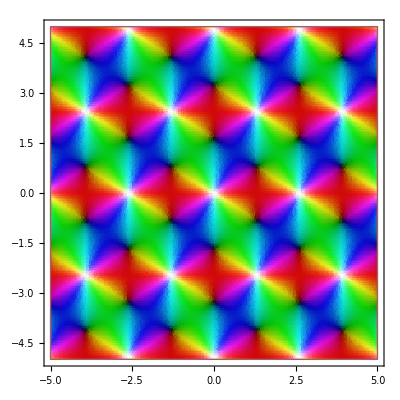

```mathematica
g[z_]:=WeierstrassP[z,{1,2}]
saturation[z_]:=Exp[3]/(Exp[3]+z)
brightness[z_]:=  5z/(1+5 z)
(*x and y range from -5 to 5, but you can adjust this*)
ParametricPlot[{x,y},{x,-5,5},{y,-5,5},ColorFunction->Function[{x,y},Hue[Arg[g[x+I y]]/(2 Pi),saturation[Abs[g[x+I y]]],brightness[Abs[g[x+ I y]]]]],ColorFunctionScaling->False,Mesh->False,Axes->False,PlotPoints->200]
```